```mathematica
scaledData = {
10^6#x,
10^6#px/#pz,
10^6#y,
10^6#py/#pz,
10^6#z,
10^-9#pz
}&/@data;
```

```mathematica
iqrRangeScale = 3;
dataRanges = {
Median[#]-iqrRangeScale*InterquartileRange[#],
Median[#]+iqrRangeScale*InterquartileRange[#]
}&/@Transpose[scaledData]
```

{{-45.9631,46.2098},{-88.8186,67.2917},{-30.467,30.4256},{-74.5342,75.9131},{-25.1723,22.5001},{9.85329,10.1466}}

```mathematica
Length[scaledData]
clippedData =Select[
scaledData,
RegionMember[
rangeCuboid = Cuboid[dataRanges[[All,1]],dataRanges[[All,2]]],
#
]&
];
Length[clippedData]
```

9798

8526

```mathematica
imageSize=800;
rasterSize = 800;
```

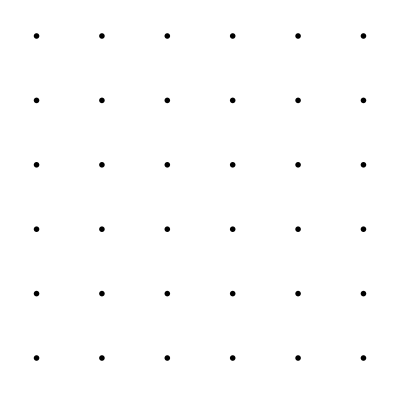

```mathematica
GraphicsGrid[
ParallelTable[
If[i!=j,
Rasterize[
densityHistogramMod[
clippedData[[All,{i,j}]],
{50,50},
ImageSize->imageSize,
PlotRange->{dataRanges[[i]],dataRanges[[j]]},
LabelStyle->20
],RasterSize->rasterSize],
Rasterize[
Histogram[
clippedData[[All,i]],
{(dataRanges[[i,2]]-dataRanges[[i,1]])/50},
ImageSize->imageSize,
PlotRange->{dataRanges[[i]],Automatic},
LabelStyle->20
],RasterSize->rasterSize]
],
{i,1,6},
{j,1,6}
]]
```